# Superimposed Kerr Metric in Kerr-Schild coordinates.

## Import metric

```mathematica
Import["~/llgsks.mx"];
Import["~/uugsks.mx"];
```

## Plot definitions

```mathematica
llgSKS=(llgSKS//.Ω->Sqrt[(M1+M2)/b^3]);
uugSKS=(uugSKS//.Ω->Sqrt[(M1+M2)/b^3]);

ClearAll[M1,M2,a1,a2,b]
M1=1;
M2=1;
a1=0;
a2=0;
b=20;
```

## Plots

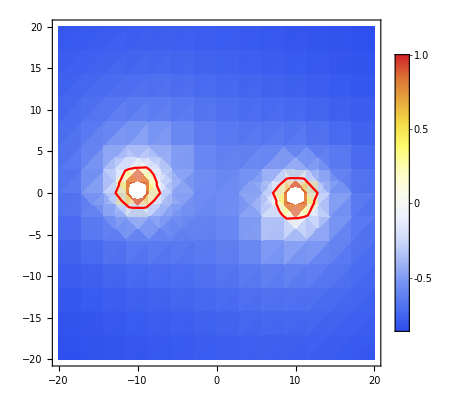

```mathematica
Show[
DensityPlot[
(llgSKS⟦1,1⟧)//.{t->0,z->0},
{x,-b,b},
{y,-b,b},

PlotPoints->15,
ColorFunction->"TemperatureMap",
PlotLegends->True,
PlotRange->{Full,Full,{-1,1}}
],

ContourPlot[
((llgSKS⟦1,1⟧)//.{t->0,z->0})==0,
{x,-b,b},
{y,-b,b},

PlotPoints->10,
ContourShading->None,
ContourStyle->Directive[Red,Thick],
PlotLegends->False,
PlotRange->{Full,Full,{-1,1}}
]
]
```

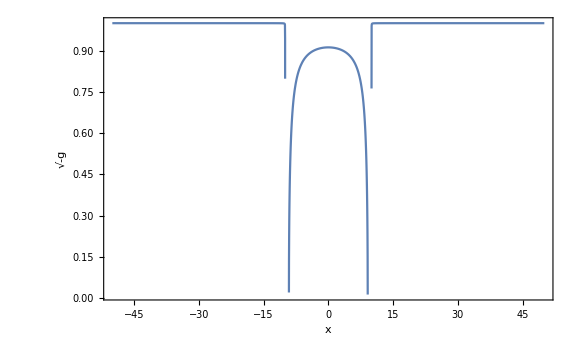

```mathematica
Plot[Sqrt[-Det[(llgSKS//.{t->0,y->0,z->0})]],{x,-50,50},PlotRange->Full,FrameLabel->{"x","√-g"},Axes->False,Frame->True,ImageSize->Large]
```

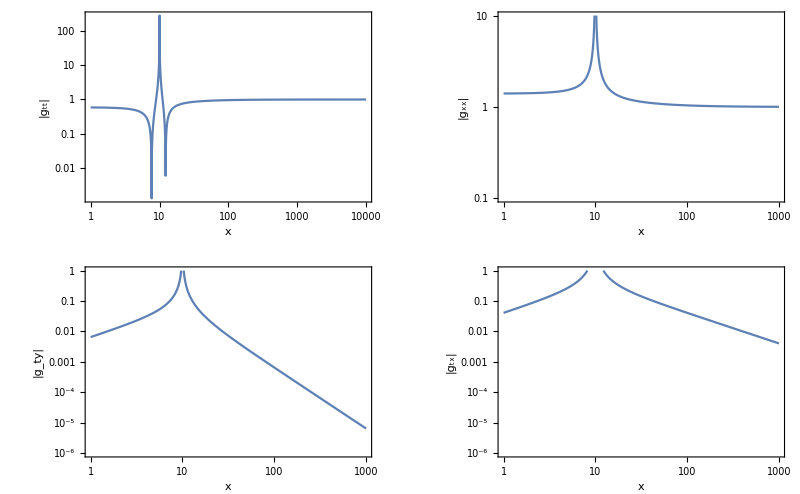

```mathematica
GraphicsGrid[
{
{
LogLogPlot[Abs[(llgSKS⟦1,1⟧//.{t->0,y->0,z->0})],{x,10^0,10^4},PlotRange->{Full,Full},FrameLabel->{"x","|g_tt|"},Axes->False,Frame->True,ImageSize->Large],
LogLogPlot[Abs[(llgSKS⟦2,2⟧//.{t->0,y->0,z->0})],{x,10^0,10^3},PlotRange->{Full,{10^-1,10^1}},FrameLabel->{"x","|g_xx|"},Axes->False,Frame->True,ImageSize->Large]
},
{
LogLogPlot[Abs[(llgSKS⟦1,3⟧//.{t->0,y->0,z->0})],{x,10^0,10^3},PlotRange->{Full,{10^-6,10^0}},FrameLabel->{"x","|g_ty|"},Axes->False,Frame->True,ImageSize->Large],
LogLogPlot[Abs[(llgSKS⟦1,2⟧//.{t->0,y->0,z->0})],{x,10^0,10^3},PlotRange->{Full,{10^-6,10^0}},FrameLabel->{"x","|g_tx|"},Axes->False,Frame->True,ImageSize->Large]
}
},
ImageSize->Full
]
```

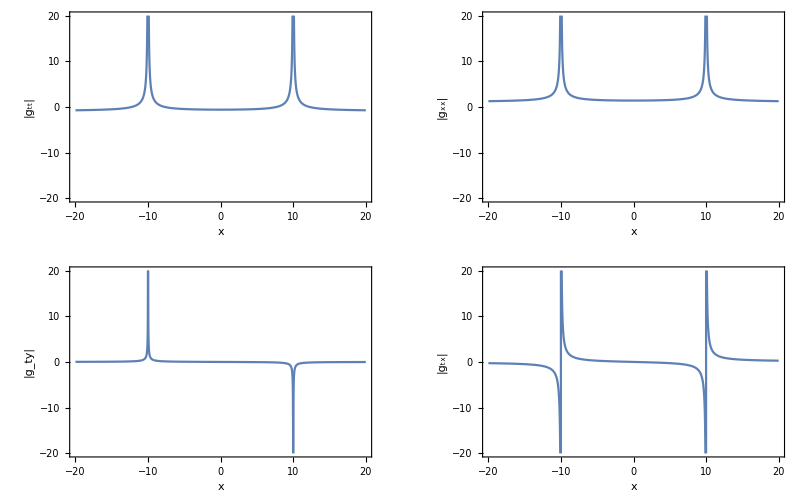

```mathematica
GraphicsGrid[
{
{
Plot[(llgSKS⟦1,1⟧//.{t->0,y->0,z->0}),{x,-b,b},PlotRange->{-b,b},FrameLabel->{"x","|g_tt|"},Axes->False,Frame->True,ImageSize->Large],
Plot[(llgSKS⟦2,2⟧//.{t->0,y->0,z->0}),{x,-b,b},PlotRange->{-b,b},FrameLabel->{"x","|g_xx|"},Axes->False,Frame->True,ImageSize->Large]
},
{
Plot[(llgSKS⟦1,3⟧//.{t->0,y->0,z->0}),{x,-b,b},PlotRange->{-b,b},FrameLabel->{"x","|g_ty|"},Axes->False,Frame->True,ImageSize->Large],
Plot[(llgSKS⟦1,2⟧//.{t->0,y->0,z->0}),{x,-b,b},PlotRange->{-b,b},FrameLabel->{"x","|g_tx|"},Axes->False,Frame->True,ImageSize->Large]
}
},
ImageSize->Full
]
```

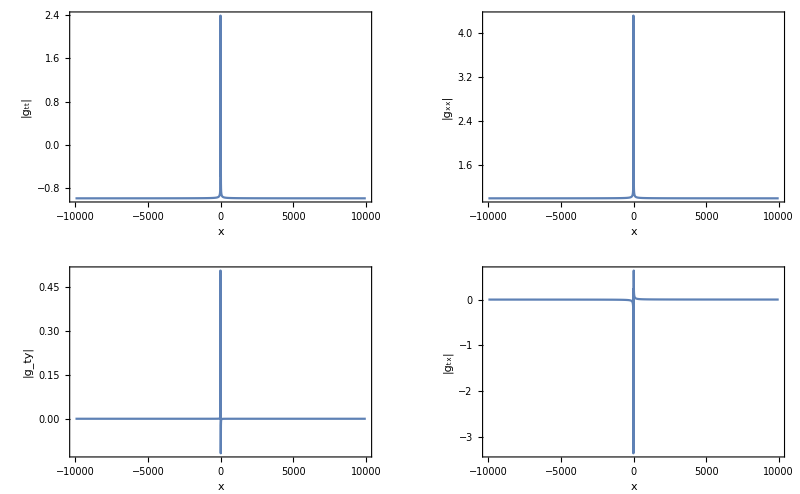

```mathematica
GraphicsGrid[
{
{
Plot[(llgSKS⟦1,1⟧//.{t->0,y->0,z->0}),{x,-10^4,10^4},PlotRange->{Full,Full},FrameLabel->{"x","|g_tt|"},Axes->False,Frame->True,ImageSize->Large],
Plot[(llgSKS⟦2,2⟧//.{t->0,y->0,z->0}),{x,-10^4,10^4},PlotRange->{Full,Full},FrameLabel->{"x","|g_xx|"},Axes->False,Frame->True,ImageSize->Large]
},
{
Plot[(llgSKS⟦1,3⟧//.{t->0,y->0,z->0}),{x,-10^4,10^4},PlotRange->{Full,Full},FrameLabel->{"x","|g_ty|"},Axes->False,Frame->True,ImageSize->Large],
Plot[(llgSKS⟦1,2⟧//.{t->0,y->0,z->0}),{x,-10^4,10^4},PlotRange->{Full,Full},FrameLabel->{"x","|g_tx|"},Axes->False,Frame->True,ImageSize->Large]
}
},
ImageSize->Full
]
```